```mathematica
Cylinder[]
```

Cylinder[{{0,0,-1},{0,0,1}}]

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
Graphics3D[Circle[]]
```

-Graphics3D-



```mathematica
Graphics[Circle[]]
```



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

RevolutionPlot3D[t^4 - t^2, {t, 0, 1}]

```mathematica
t^4-t^2
```

-t^2+t^4

```mathematica
Simplify[-t^2+t^4]
```

t^2 (-1+t^2)

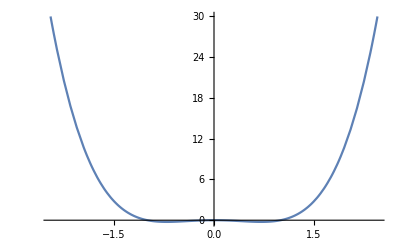

```mathematica
Plot[t^2 (-1+t^2),{t,-2.449489742783178,2.449489742783178}]
```

```mathematica
RevolutionPlot3D[t^4 - t^2, {t, 0, 1}]
```

-Graphics3D-

```mathematica
Sin[x]Sin[x]-Sin[x]x
```

-x Sin[x]+Sin[x]^2

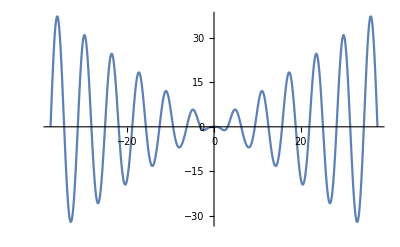

```mathematica
Plot[-x Sin[x]+Sin[x]^2,{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
RevolutionPlot3D[-x Sin[x]+Sin[x]^2, {x, 0, 1}]
```

-Graphics3D-

```mathematica
Manipulate[
RevolutionPlot3D[-x Sin[x]+Sin[x]^2, {x, 0, a π/4}],
{a, 1, 10, 1}]
```

```mathematica
RevolutionPlot3D[-x Sin[x]+Sin[x]^2, {x, 0, 1}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[-x Sin[x]+Sin[x]^2, {x, 0, 1}]
```

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Cos[t],Sin[t]},{t,0,2π}]
```

-Graphics3D-

```mathematica
{2+Cos[t],Sin[t]}
```

{2+Cos[t],Sin[t]}

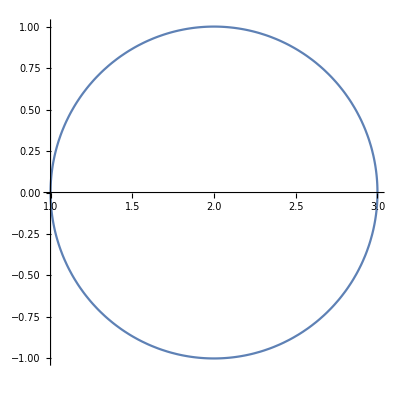

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,2π}]
```

```mathematica
RevolutionPlot3D[{Sin[t],t},{t,0,2 Pi},{θ,0,Pi}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[t],t},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[1/t,{t,0,1}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Tooltip[{t,t},"cone"],{t,-2,2},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[t]+Sin[5 t]/10,Cos[t]+Cos[5 t]/10},{t,0,Pi},Mesh->10,MeshStyle->{Cyan,Directive[Green,Dashed]},PlotStyle->Gray]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[t,{t,0,2 Pi},BoundaryStyle->Red,RegionFunction->Function[{x,y,z,t,θ},Sin[3 t] Sin[3 θ]>0]]
```

-Graphics3D-

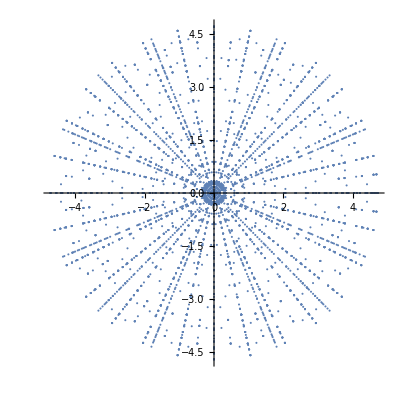

```mathematica
ListPolarPlot[Reap[RevolutionPlot3D[Cos[t],{t,0,3 Pi/2},{θ,0,2 Pi},EvaluationMonitor:>Sow[{θ,t}]]][[-1,1]]]
```

```mathematica
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}]
```

-Graphics3D-

```mathematica
ListPlot3D[{{1,1,1}}]
```

ListPlot3D::gmat: {{1.,1.,1.}} is not a rectangular array larger than 2 x 2.

ListPlot3D[{{1,1,1}}]

```mathematica
ListPlot3D[{{0,0,1},{1,0,0},{0,1,0}},Mesh->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{{0,0,1},{1,0,0}},Mesh->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{{0,0,1},{1,0,0}}]
```

-Graphics3D-

```mathematica
ListPlot3D[{{0,0,1}}]
```

ListPlot3D::gmat: {{0.,0.,1.}} is not a rectangular array larger than 2 x 2.

ListPlot3D[{{0,0,1}}]

```mathematica
ListPlot3D[data,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

ListPlot3D::arrayerr: data must be a valid array or a list of valid arrays.

ListPlot3D[data,Mesh→None,InterpolationOrder→3,ColorFunction→SouthwestColors]

```mathematica
Show[Plot3D[(y^2/x),{x,-3,3},{y,-3,3},PlotStyle->Opacity[0.3]],Graphics3D[{Red,PointSize[0.1],Point[{0,0,0}]}]]
```

-Graphics3D-

```mathematica
Graphics3D[Point[]]
```

-Graphics3D-

```mathematica
Graphics3D[Point[{0, 0, 0}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[j^2+i],{i,0,3,0.1},{j,0,3,0.1}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[i] Cos[j],{i,-5,5,.25},{j,-5,5,.25}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Point[{0,0,0}]}]
```

Show[{-Graphics3D-,Point[{0,0,0}]}]

```mathematica
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[Point[{0,0,0}]]}, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[Point[{0,0,-1}]]}, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[Point[{1,1,1}]]}, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[Point[{a,b,√(1-a^2-b^2)}]]}, AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1}]
```

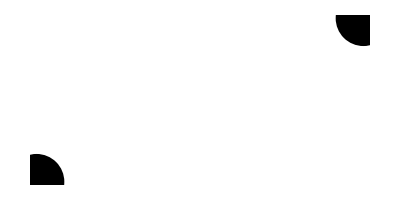

```mathematica
Graphics[{PointSize[0.1],Point[{{0,0},{2,1}},VertexColors->{Red,Green}]}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[Point[{a,b,√(1-a^2-b^2)}]]}, AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1}]
```

```mathematica
Graphics3D[{PointSize[0.1],Point[{{0,0, 0}},VertexColors->Red]}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}],
{a, 0, π}, {b, 0, π}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}],
{a, 0, 1}, {b, 0, 1-a}]
```

```mathematica
Graphics3D[Polygon[Table[rantricoords,{10000}]]]
```

-Graphics3D-

```mathematica
rantricoords:=Table[rcoord,{3}]
```

```mathematica
Graphics3D[{Polygon[{{0,0,0},{0,0,1},{1,1,0},{1,0,1}}]}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Polygon[{{0,0,0},{0,0,1},{1,1,0},{1,0,1}}]}],Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->Red}]},
AxesLabel->{x,y,z}, Boxed->False[]],
{a, 0, 1}, {b, 0, 1-a}]
```

```mathematica
\[FreakedSmiley]
```

\[FreakedSmiley]

```mathematica
Remove[\[FreakedSmiley]]
```

Remove::rmptc: Symbol \[FreakedSmiley] is Protected and cannot be removed.

```mathematica
Protect[\[FreakedSmiley]]
```

{\[FreakedSmiley]}

```mathematica
Information[\[FreakedSmiley]]
```

Global`\[FreakedSmiley]

```mathematica
Unprotect[\[FreakedSmiley]]
```

{\[FreakedSmiley]}

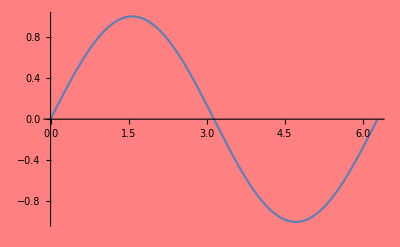

```mathematica
g1=Plot[Sin[x],{x,0,2 Pi}];
Show[g1,Background->Pink]
```

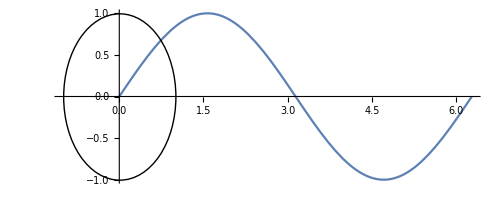

```mathematica
Show[{g1,Graphics[Circle[]]},PlotRange->All,AspectRatio->Automatic]
```

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0}};
```

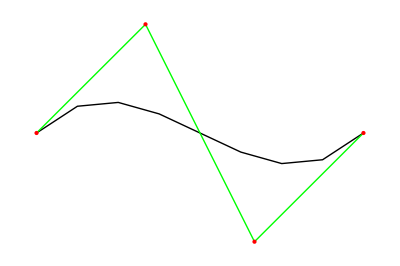

```mathematica
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
```

```mathematica
Graphics[{BSplineCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics-

```mathematica
pts={{0,0,0},{1,1,1},{2,-1,1},{3,0,2},{4,1,1}};
```

```mathematica
Graphics3D[{BSplineCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics3D-

```mathematica
Show[%78,Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[Ball[{0,0,0}]],Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}],VertexColors->{Red}}]},
AxesLabel->{x,y,z}, Boxed->False[]],
{a, 0, 1}, {b, 0, 1-a}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[ϕ]Sin[θ], Sin[θ]Sin[ϕ],Cos[θ]},
{θ, 0, 2π}, {ϕ, 0, π}],
Graphics3D[{PointSize[0.1],Point[{a,b, √(1-a^2-b^2)}]}],
Graphics3D[{PointSize[0.1],Point[{c,d, √(1-c^2-d^2)}]}]},
AxesLabel->{x,y,z}, Boxed->False[]],
{{a,1}, 0, 1}, {b, 0, 1-a},
{c, 0, 1}, {d, 0, 1-c}]
```